# Sphere Tetrahedron Picking

### Author

Eric W. Weisstein
March 14, 2017

This notebook downloaded from http://mathworld.wolfram.com/notebooks/ComputationalGeometry/SphereTetrahedronPicking.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/SphereTetrahedronPicking.html.

©2017 Wolfram Research, Inc. except for portions noted otherwise

## Area of a Random Triangle

```mathematica
TetrahedronVolume[{x1_,x2_,x3_,x4_}]:=Module[{i={1,1,1,1}},Det[Join[Transpose[{x1,x2,x3,x4}],{i}]]/3!]
```

### Exact

```mathematica
4/105 π//N
```

0.11968

```mathematica
mu
```

0.119644

#### Attempt to Guess

```mathematica
v=RootApproximant[mu/π,1]
```

801006/21032747

```mathematica
4/105 π
```

```mathematica
N[v-4/105]
```

-0.0000114823

```mathematica
v=Rationalize[mu/π,.001]
```

1/26

```mathematica
N[v-4/105]
```

0.0003663

```mathematica
{4/105.,1/26.}
```

{0.0380952,0.0384615}

```mathematica
WolframAlpha["0.11964",{{"PossibleClosedForm",3},"FormattedData"}]
```

(4 π)/105≈0.119679720

### RandomPoint

```mathematica
tet=RandomPoint[Sphere[],{10^6,4}];//Timing
```

{0.436551,Null}

```mathematica
Length[vols=Abs[TetrahedronVolume/@tet]]//Timing
```

{13.8723,1000000}

```mathematica
TimeConstrained[Length[vols=Volume[Tetrahedron[#]]&/@tet],60]//Timing
```

{60.3168,$Aborted}

```mathematica
TimeConstrained[Length[vols=RegionMeasure[Tetrahedron[#]]&/@tet],60]//Timing
```

{60.2907,$Aborted}

bug(330535): Area, Volume, and RegionMeasure should be faster on shape primitives

```mathematica
Through[{Mean,Variance}[vols]]
```

{0.119641,0.0103641}

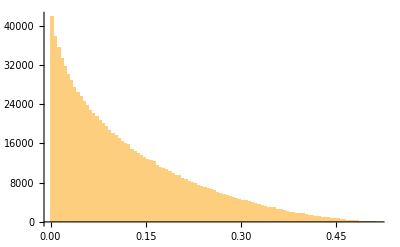

```mathematica
Histogram[vols,100]
```

### Monte Carlo

```mathematica
SphericalDistribution[num_]:=Table[{Cos[#1]Sqrt[1-#2^2],Sin[#1]Sqrt[1-#2^2],#2}&[Random[Real,{0,2Pi}],Random[Real,{-1,1}]],{num}]
```

```mathematica
Length[pts=Abs/@TetrahedronVolume/@Partition[SphericalDistribution[10^7],4]]//Timing
```

{169.654,2500000}

```mathematica
{mu,var}=Through[{Mean,Variance}[pts]]
```

{0.119644,0.0103572}

```mathematica
mu^2-(2/81)^2
```

0.0137049

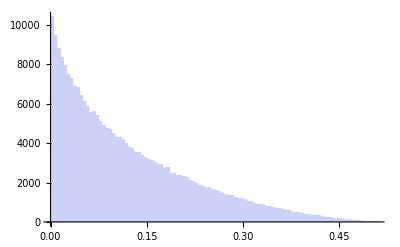

```mathematica
Histogram[pts]
```

## Distances using (u, v)

```mathematica
r[u_,v_]:=With[{θ=2π u,ϕ=ArcCos[2v-1]},
{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
]
```

```mathematica
{r[0,1],r[0,v1]}//Simplify
```

{{0,0,1},{2 √(-(-1+v1) v1),0,-1+2 v1}}

```mathematica
voluv=FullSimplify[TetrahedronVolume[{r[0,1],r[0,v2],r[u3,v3],r[u4,v4]}],And@@(0<#<1&/@{v2,u3,v3,u4,v4})]
```

-4/3 (√((-1+v2) v2 (-1+v3) v3) (-1+v4) Sin[2 π u3]-(-1+v2) √((-1+v3) v3 (-1+v4) v4) Sin[2 π (u3-u4)]-(-1+v3) √((-1+v2) v2 (-1+v4) v4) Sin[2 π u4])

```mathematica
voluv=-4/3 (√((-1+v2) v2 (-1+v3) v3) (-1+v4) Sin[2 π u3]-(-1+v2) √((-1+v3) v3 (-1+v4) v4) Sin[2 π (u3-u4)]-(-1+v3) √((-1+v2) v2 (-1+v4) v4) Sin[2 π u4]);
```

```mathematica
<<Utilities`Simplify`
```

```mathematica
Flatten[t/.Table[Solve[Recognize[a,1,t,10^n]==0,t],{n,5,15}]]
```

{53870/450117,53870/450117,6687/55874,6687/55874,374/3125,374/3125,45/376,45/376,14/117,3/25,3/25}

```mathematica
N[%,10]
```

{0.1196799943,0.1196799943,0.1196799943,0.1196799943,0.11968,0.11968,0.1196808511,0.1196808511,0.1196581197,0.12,0.12}

### Numerical

#### v5.2

```mathematica
NIntegrate[Abs[voluv],{v2,0,1},{u3,0,1},{v3,0,1},{u4,0,1},{v4,0,1},Method->QuasiMonteCarlo]//Timing
```

{0.152657 Second,0.119701}

```mathematica
NIntegrate[Abs[voluv],{v2,0,1},{u3,0,1},{v3,0,1},{u4,0,1},{v4,0,1},Method->QuasiMonteCarlo,PrecisionGoal->3,MaxPoints->10^6]//Timing
```

{14.8106 Second,0.119678}

```mathematica
NIntegrate[Abs[voluv],{v2,0,1},{u3,0,1},{v3,0,1},{u4,0,1},{v4,0,1},Method->QuasiMonteCarlo,PrecisionGoal->4,MaxPoints->10^7]//Timing
```

{453.42 Second,0.11968}

#### v6

```mathematica
NIntegrate[Abs[voluv],{v2,0,1},{u3,0,1},{v3,0,1},{u4,0,1},{v4,0,1}]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 1000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the difference between the values of PrecisionGoal and WorkingPrecision is too small; the integrand is highly oscillatory or it is not a (piecewise) smooth function; the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxNumberOfErrorIncreases might lead to a convergent numerical integration.

{12.1468 Second,0.11972}

```mathematica
NIntegrate[Abs[voluv],{v2,0,1},{u3,0,1},{v3,0,1},{u4,0,1},{v4,0,1},Method->{SymbolicPreprocessing,Method->QuasiMonteCarlo}]//Timing
```

{0.511357 Second,0.119915}

```mathematica
NIntegrate[Abs[voluv],{v2,0,1},{u3,0,1},{v3,0,1},{u4,0,1},{v4,0,1},Method->{SymbolicPreprocessing,Method->QuasiMonteCarlo},PrecisionGoal->3,MaxPoints->10^6]//Timing
```

NIntegrate::mccnv: The integral failed to converge after 1000000 iterations. More…

{18.2877 Second,0.119681}

```mathematica
NIntegrate[Abs[voluv],{v2,0,1},{u3,0,1},{v3,0,1},{u4,0,1},{v4,0,1},Method->{SymbolicPreprocessing,Method->AdaptiveQuasiMonteCarlo},PrecisionGoal->3,MaxPoints->10^6]//Timing
```

{14.1866 Second,0.119716}

```mathematica
NIntegrate[Abs[voluv],{v2,0,1},{u3,0,1},{v3,0,1},{u4,0,1},{v4,0,1},Method->{SymbolicPreprocessing,Method->AdaptiveQuasiMonteCarlo},PrecisionGoal->4,MaxPoints->10^7]//Timing
```

NIntegrate::mccnv: The integral failed to converge after 10000100 iterations. More…

{206.06 Second,0.119691}

### Analytic

```mathematica
Timing[i1=Integrate[Sqrt[v^2],{v3,0,1}]]
```

{208.98 Second,∫_0^1 4/3 √(√((-1+v2) v2 (-1+v3) v3) (-1+v4) Sin[2 π u3]-(-1+v2) √((-1+v3) v3 (-1+v4) v4) Sin[2 π (u3-u4)]-(-1+v3) √((-1+v2) v2 (-1+v4) v4) Sin[2 π u4])^2ⅆv3}

```mathematica
Timing[i1=Integrate[Sqrt[v^2],{v3,0,1}]]
```

```mathematica
4/3 Integrate[Sqrt[v^2],{v2,0,1}]
```

```mathematica
Timing[i1=Integrate[Sqrt[v^2],{u3,0,1}]]
```

-(4 √((-1+v2) v2 (-1+v4) v4) √(((-1+v3) √((-1+v2) v2 (-1+v4) v4)-(-1+v2) √((-1+v3) v3 (-1+v4) v4))^2 Sin[2 π u4]^2))/(3 (-√((-1+v2) v2 (-1+v4) v4)+v3 √((-1+v2) v2 (-1+v4) v4)+√((-1+v3) v3 (-1+v4) v4)-v2 √((-1+v3) v3 (-1+v4) v4)))+(4 v3 √((-1+v2) v2 (-1+v4) v4) √(((-1+v3) √((-1+v2) v2 (-1+v4) v4)-(-1+v2) √((-1+v3) v3 (-1+v4) v4))^2 Sin[2 π u4]^2))/(3 (-√((-1+v2) v2 (-1+v4) v4)+v3 √((-1+v2) v2 (-1+v4) v4)+√((-1+v3) v3 (-1+v4) v4)-v2 √((-1+v3) v3 (-1+v4) v4)))

```mathematica
NIntegrate[i1,{v2,0,1},{v3,0,1},{u4,0,1},{v4,0,1},Method->QuasiMonteCarlo]
```

NIntegrate::mccnv: The integral failed to converge after 50000 iterations. More…

0.0245522

...wrong..

```mathematica
Timing[i1=Integrate[Sqrt[v^2],{v3,0,1}]]
```

{208.98 Second,∫_0^1 4/3 √(√((-1+v2) v2 (-1+v3) v3) (-1+v4) Sin[2 π u3]-(-1+v2) √((-1+v3) v3 (-1+v4) v4) Sin[2 π (u3-u4)]-(-1+v3) √((-1+v2) v2 (-1+v4) v4) Sin[2 π u4])^2ⅆv3}

```mathematica
Timing[i1=Integrate[Sqrt[v^2],{v3,0,1}]]
```

```mathematica
4/3 Integrate[Sqrt[v^2],{v2,0,1}]
```

## Distances using (u, θ)

```mathematica
r[θ_,u_]:={Sqrt[1-u^2]Cos[θ],Sqrt[1-u^2]Sin[θ],u}
```

```mathematica
{r[0,1],r[0,u]}
```

{{0,0,1},{√(1-u^2),0,u}}

```mathematica
v=TetrahedronVolume[{r[0,1],r[0,u2],r[θ3,u3],r[θ4,u4]}]
```

1/6 (-√(1-u3^2) (-√(1-u2^2) (1-u4)+(1-u2) √(1-u4^2) Cos[θ4]) Sin[θ3]+√(1-u4^2) (-√(1-u2^2) (1-u3)+(1-u2) √(1-u3^2) Cos[θ3]) Sin[θ4])

```mathematica
v//InputForm
```

(-(Sqrt[1 - u3^2]*(-(Sqrt[1 - u2^2]*(1 - u4)) + (1 - u2)*Sqrt[1 - u4^2]*Cos[θ4])*
    Sin[θ3]) + Sqrt[1 - u4^2]*(-(Sqrt[1 - u2^2]*(1 - u3)) + 
    (1 - u2)*Sqrt[1 - u3^2]*Cos[θ3])*Sin[θ4])/6

```mathematica
v=1/6 (-√(1-u3^2) (-√(1-u2^2) (1-u4)+(1-u2) √(1-u4^2) Cos[θ4]) Sin[θ3]+√(1-u4^2) (-√(1-u2^2) (1-u3)+(1-u2) √(1-u3^2) Cos[θ3]) Sin[θ4]);
```

```mathematica
vol=1/(6 √(1-v1^2)) (-√(1-u3^2) (-√(1-u2^2) (1-u4)+(1-u2) √(1-u4^2) Cos[θ4]) √(1-v1^2)+√(1-u4^2) (-√(1-u2^2) (1-u3)+(1-u2) √(1-u3^2)v1)Sin[θ4]);
```

### Numerical

#### v5.x

```mathematica
1/(16 π^2)NIntegrate[Abs[vol],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{θ4,0,2π},Method->QuasiMonteCarlo,MaxPoints->10^6]//Timing
```

{2.47391 Second,0.119857}

```mathematica
1/(16 π^2)NIntegrate[Abs[vol],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{θ4,0,2π},Method->QuasiMonteCarlo,MaxPoints->10^6,PrecisionGoal->3]//Timing
```

NIntegrate::mccnv: The integral failed to converge after 1000000 iterations. More…

{24.5185 Second,0.119772}

#### v6

```mathematica
1/(16 π^2)NIntegrate[Abs[vol],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{θ4,0,2π}]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 1000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the difference between the values of PrecisionGoal and WorkingPrecision is too small; the integrand is highly oscillatory or it is not a (piecewise) smooth function; the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxNumberOfErrorIncreases might lead to a convergent numerical integration.

{37.403 Second,0.119708}

```mathematica
1/(16 π^2)NIntegrate[Abs[vol],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{θ4,0,2π},Method->{SymbolicPreprocessing,Method->QuasiMonteCarlo}]//Timing
```

NIntegrate::mccnv: The integral failed to converge after 50000 iterations. More…

{1.84721 Second,0.119822}

```mathematica
1/(16 π^2)NIntegrate[Abs[vol],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{θ4,0,2π},Method->{SymbolicPreprocessing,Method->AdaptiveQuasiMonteCarlo},PrecisionGoal->3]//Timing
```

{25.2049 Second,0.117241}

### Numerical splitting into Two parts

```mathematica
vol1=1/(6 √(1-v2^2)√(1-v1^2)) (-√(1-u3^2) (-√(1-u2^2) (1-u4)+(1-u2) √(1-u4^2) v2) √(1-v1^2)+√(1-u4^2) (-√(1-u2^2) (1-u3)+(1-u2) √(1-u3^2)v1)√(1-v2^2));
```

```mathematica
vol2=1/(6 √(1-v2^2)√(1-v1^2)) (-√(1-u3^2) (-√(1-u2^2) (1-u4)+(1-u2) √(1-u4^2) v2) √(1-v1^2)+√(1-u4^2) (-√(1-u2^2) (1-u3)+(1-u2) √(1-u3^2)v1)(-1)√(1-v2^2));
```

#### v5.x

```mathematica
i1=1/(16 π^2)NIntegrate[Abs[vol1],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{v2,-1,1},Method->QuasiMonteCarlo,MaxPoints->10^6]
```

0.0469612

```mathematica
i2=1/(16 π^2)NIntegrate[Abs[vol2],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{v2,-1,1},Method->QuasiMonteCarlo,MaxPoints->10^6]
```

0.0726174

```mathematica
i1+i2
```

0.119579

#### v6

```mathematica
i1=1/(16 π^2)NIntegrate[Abs[vol1],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{v2,-1,1}]
```

$Aborted

```mathematica
i1=1/(16 π^2)NIntegrate[Abs[vol1],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{v2,-1,1},Method->{SymbolicPreprocessing,Method->QuasiMonteCarlo}]
```

$Aborted

```mathematica
i2=1/(16 π^2)NIntegrate[Abs[vol2],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{v2,-1,1}]
```

$Aborted

```mathematica
i2=1/(16 π^2)NIntegrate[Abs[vol2],{u2,-1,1},{u3,-1,1},{u4,-1,1},{v1,-1,1},{v2,-1,1},Method->{SymbolicPreprocessing,Method->QuasiMonteCarlo}]
```

$Aborted

### Normalization

```mathematica
Integrate[1,{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,2Pi},{θ4,0,2Pi}]
```

32 π^2

### μ'_1

```mathematica
1/(32 π^2)NIntegrate[Evaluate[Abs[v]],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,2Pi},{θ4,0,2Pi},Method->QuasiMonteCarlo,PrecisionGoal->3,MaxPoints->10^6]//Timing
```

{15.48 Second,0.119683}

```mathematica
1/(16 π^2)NIntegrate[Evaluate[Abs[v]],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi},Method->QuasiMonteCarlo,PrecisionGoal->3,MaxPoints->10^6]//Timing
```

{14.81 Second,0.119682}

```mathematica
1/(16 π^2)NIntegrate[Evaluate[Sqrt[v^2]],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi},Method->QuasiMonteCarlo,PrecisionGoal->3,MaxPoints->10^6]//Timing
```

{11.34 Second,0.119682}

```mathematica
1/(16 π^2)NIntegrate[Evaluate[Abs[v]],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi},Method->QuasiMonteCarlo,PrecisionGoal->4,MaxPoints->10^7]//Timing
```

NIntegrate::mccnv: The integral failed to converge after 10000000 iterations. More…

{273.17 Second,0.11968}

```mathematica
1/(16 π^2)NIntegrate[Evaluate[Abs[v]],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi}]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

```mathematica
1/(16 π^2)NIntegrate[Evaluate[Abs[v]],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi},Method->MultiDimensional]//Timing
```

#### v4.2

```mathematica
1/(16 π^2)Integrate[Sqrt[v^2],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi}]//Timing
```

Roots::neq: 1 - √4 + 4\ (-1 - u2)\ (1 - u2) + u2^2 is expected to be a polynomial in the variable u2.

Last::normal: Nonatomic expression expected at position 1 in Last[u2].

Roots::eqn: 0 is not an equation.

Roots::neq: 1 - √4 + 4\ (-1 - u2)\ (1 - u2) + u2^2 is expected to be a polynomial in the variable u2.

Last::normal: Nonatomic expression expected at position 1 in Last[u2].

Roots::eqn: 0 is not an equation.

Roots::neq: -2 - 6\ u2^2 + 3\ √4 + 4\ (-1 + u2)\ (1 + u2) + u2^2\ √4 + 4\ (-1 + u2)\ (1 + u2) is expected to be a polynomial in the variable u2.

General::stop: Further output of Roots :: "neq" will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[u2].

General::stop: Further output of Last :: "normal" will be suppressed during this calculation.

Roots::eqn: 0 is not an equation.

General::stop: Further output of Roots :: "eqn" will be suppressed during this calculation.

{406.27 Second,(ⅈ (π^2 Log[-ⅈ √2]-π^2 Log[ⅈ √2]+3 π^2 Log[-2 ⅈ √2]-3 π^2 Log[2 ⅈ √2]))/(192 π^2)}

```mathematica
FullSimplify[1/(192 π^2)(ⅈ (π^2 Log[-ⅈ √2]-π^2 Log[ⅈ √2]+3 π^2 Log[-2 ⅈ √2]-3 π^2 Log[2 ⅈ √2]))]
```

π/48

```mathematica
N[π/48]
```

0.0654498

...wrong...

#### v5

```mathematica
1/(16 π^2)Integrate[Sqrt[v^2],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi}]//Timing
```

{210.68 Second,π/192}

```mathematica
N[Pi/192]
```

0.0163625

...wrong...

#### v6

```mathematica
1/(16 π^2)Integrate[Sqrt[v^2],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi}]//Timing
```

{231.45 Second,π/96}

```mathematica
N[Pi/96]
```

0.0327249

...wrong...

```mathematica
1/(16 π^2)NIntegrate[Sqrt[v^2],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,π},{θ4,0,2π},Method->QuasiMonteCarlo,MaxPoints->10^6]
```

0.119599

#### By Pieces: u_2

```mathematica
Timing[i1=1/(16 π^2)Integrate[Sqrt[v^2],{u2,-1,1},Assumptions->-1<u3<1&&-1<u4<1&&0<θ3<π&&0<θ4<2π]]
```

```mathematica
NIntegrate[Evaluate[i1],{u3,-1,1},{u4,-1,1},{θ3,0,π},{θ4,0,2π},Method->QuasiMonteCarlo,MaxPoints->10^6]//Timing
```

#### By Pieces: u_3(v5)

```mathematica
Timing[i1=Simplify[1/(16 π^2)Integrate[Sqrt[v^2],{u3,-1,1},Assumptions->-1<u2<1&&-1<u4<1&&0<θ3<π&&0<θ4<2π]]]
```

{336.76 Second,((-1+u2) (-1+u4) ((Abs[√(1-u2^2) (-1+u4) Sin[θ3]-(-1+u2) √(1-u4^2) Sin[θ3-θ4]] (-ⅈ (1+u2) √(1-u4^2) Log[-2 ⅈ √(1-u2^2)] Sin[θ3]+(1+u4) (ⅈ √(1-u2^2) Log[-2 ⅈ √(1-u4^2)] Sin[θ3-θ4]+(1+u2) Sin[θ4])))/(√(1-u2^2) (-1+u4) Sin[θ3]-(-1+u2) √(1-u4^2) Sin[θ3-θ4])+Abs[Sin[θ4]] Csc[θ4] (ⅈ (1+u2) √(1-u4^2) Log[2 ⅈ √(1-u2^2)] Sin[θ3]+(1+u4) (-ⅈ √(1-u2^2) Log[2 ⅈ √(1-u4^2)] Sin[θ3-θ4]+3 (1+u2) Sin[θ4]))))/(192 π^2 √((-1+u2^2) (-1+u4^2)))}

```mathematica
NIntegrate[Evaluate[i1],{u2,-1,1},{u4,-1,1},{θ3,0,π},{θ4,0,2π},Method->QuasiMonteCarlo,MaxPoints->10^6]//Timing
```

{0.37 Second,0.0972437+0.0158863 ⅈ}

#### By Pieces: u_4(v5)

```mathematica
Timing[i1=Simplify[1/(16 π^2)Integrate[Sqrt[v^2],{u4,-1,1},Assumptions->-1<u2<1&&-1<u3<1&&0<θ3<π&&0<θ4<2π]]]
```

{373.27 Second,((-1+u2) (-1+u3) (3 (1+u2) (1+u3) Sin[θ3]+ⅈ (√(1-u2^2) (1+u3) Log[2 ⅈ √(1-u3^2)] Sin[θ3-θ4]+(1+u2) √(1-u3^2) Log[2 ⅈ √(1-u2^2)] Sin[θ4])+(Abs[(-1+u2) √(1-u3^2) Sin[θ3-θ4]+√(1-u2^2) (-1+u3) Sin[θ4]] ((1+u2) (1+u3) Sin[θ3]-ⅈ (√(1-u2^2) (1+u3) Log[-2 ⅈ √(1-u3^2)] Sin[θ3-θ4]+(1+u2) √(1-u3^2) Log[-2 ⅈ √(1-u2^2)] Sin[θ4])))/((-1+u2) √(1-u3^2) Sin[θ3-θ4]+√(1-u2^2) (-1+u3) Sin[θ4])))/(192 π^2 √((-1+u2^2) (-1+u3^2)))}

```mathematica
NIntegrate[Evaluate[i1],{u2,-1,1},{u3,-1,1},{θ3,0,π},{θ4,0,2π},Method->QuasiMonteCarlo,MaxPoints->10^6]//Timing
```

{0.37 Second,0.0973353+0.0158699 ⅈ}

#### By Pieces: θ_3

```mathematica
Timing[i1=Simplify[1/(16 π^2)Integrate[Sqrt[v^2],{θ3,0,Pi},Assumptions->-1<u2<1&&-1<u3<1&&-1<u4<1&&0<θ4<2π]]]
```

1/(96 π^2)(Abs[Sin[θ4]] (-π (-1+u3) √((-1+u2^2) (-1+u4^2))-(-1+u2) √((-1+u3^2) (-1+u4^2)) Cot[θ4]+√((-1+u2^2) (-1+u3^2)) (-1+u4) Csc[θ4]+(√(1-u3^2) Abs[√(1-u2^2) (-1+u3)-(-1+u2) √(1-u3^2)] (√(1-u2^2) (-1+u4)-(-1+u2) √(1-u4^2) Cos[θ4]) Csc[θ4])/(√(1-u2^2)-√(1-u2^2) u3-√(1-u3^2)+u2 √(1-u3^2))))

```mathematica
NIntegrate[Evaluate[i1],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ4,0,2π},Method->QuasiMonteCarlo,MaxPoints->10^6]//Timing
```

{0.51 Second,0.0653916}

#### By Pieces: θ_4

```mathematica
i1=1/(16 π^2)Integrate[Sqrt[v^2],{θ4,0,2Pi},Assumptions->-1<u2<1&&-1<u3<1&&-1<u4<1&&0<θ3<π]
```

(√((-1+u2^2) (-1+u3^2)) (-1+u4) Abs[√(1-u2^2) (-1+u4)-(-1+u2) √(1-u4^2)] Sin[θ3])/(48 π (-√(1-u2^2)+√(1-u2^2) u4+√(1-u4^2)-u2 √(1-u4^2)))

```mathematica
NIntegrate[Evaluate[i1],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,π},Method->QuasiMonteCarlo,MaxPoints->10^6]
```

0.0245188

..wrong..

#### Attempt to CAD

```mathematica
Simplify`PiecewiseIntegrate;
PiecewiseDump`$ShowIntegrals=True;
i=Integrate[Abs[v],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,2Pi},{θ4,0,2Pi}];//Timing
```

...ran for 10 hours using 246 MB with no result...

```mathematica
Simplify`PiecewiseIntegrate;
PiecewiseDump`$ShowIntegrals=True;
i=Integrate[Abs[v],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi}];//Timing
```

```mathematica
Timing[
i=Integrate[Abs[v],{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,2Pi},{θ4,0,2Pi}]
]
```

...crash...

### μ'_2

```mathematica
1/(16 π^2)Integrate[v^2,{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi}]//Simplify//Timing
```

2/81

### μ'_4

```mathematica
1/(16 π^2)Integrate[v^4,{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi}]//Simplify//Timing
```

{121.07 Second,4/2025}

### μ'_6

```mathematica
1/(16 π^2)Integrate[v^6,{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi}]//Simplify//Timing
```

{1693.33 Second,208/893025}

### μ'_8

```mathematica
1/(16 π^2)Integrate[v^8,{u2,-1,1},{u3,-1,1},{u4,-1,1},{θ3,0,Pi},{θ4,0,2Pi}]//Simplify//Timing
```

{2040.33 Second,4352/130203045}